```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"n_dot_pardot_crsdot_crsseldot.dat"}]]
```

{{n,time_dot,time_pardot,time_crsdot,time_crsseldot},{0,0,0.888733,0.107265,0.101728},{1000,0,9.27634,0.600584,0.102932},{2000,0,11.1898,0.818467,0.083087},{3000,0,13.6972,1.4497,0.064274},{4000,0,13.5358,1.65899,0.055501},{5000,0,13.9311,2.23886,0.055885},{6000,0,16.0227,2.84288,0.066623},{7000,0,17.2924,2.86297,0.076295},{8000,0,16.966,3.08749,0.08367},{9000,0,17.473,3.6365,0.098136}}

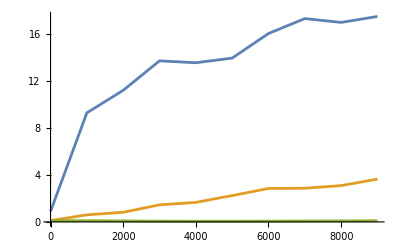

```mathematica
ListPlot[
{Transpose[{data[[2;;,1]],data[[2;;,3]]}],
Transpose[{data[[2;;,1]],data[[2;;,4]]}],
Transpose[{data[[2;;,1]],data[[2;;,5]]}]}
,Joined->True
]
```